```mathematica
(* Initialization stuff; of no intrinsic interest *)
ClearAll["Global`*"];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
(* If running from shell, must start from inside same directory in which notebook resides so that $InitialDirectory has the right value *)
(* Method of displaying figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
(* Current working directory should correspond to appropriate location now whether running from shell or notebook *)
Get["./init.m"];
(* Configure various parameters *)
FigDir="../../Figures";
```

```mathematica
kBarOptimal=((Ξ ℶ-1)/ε)^(1/(ε-1));
kBarActual=(Ξ(1+β)/((1-ε)β))^(1/(ε-1));
```

```mathematica
((-1+Ξ ℶ)/ε)^(1/(-1+ε))
```

((-1+Ξ ℶ)/ε)^(1/(-1+ε))

```mathematica
NextStepk[k_] := 𝒬 k^ε;
NextStepArrows[k_,HeadSize_] := Show[
Graphics[{Thickness[Medium],Arrowheads[{{HeadSize,1,-Graphics-}}],Arrow[{{k,NextStepk[k]},{NextStepk[k],NextStepk[k]}}]}],Graphics[{Thickness[Medium],Arrowheads[{{HeadSize,1,-Graphics-}}],Arrow[{{NextStepk[k],NextStepk[k]},{NextStepk[k],NextStepk[NextStepk[k]]}}]}]];
```

```mathematica
ε = 0.33; (* Elasticity of output with respect to capital/labor ratio; 'capital share' *)
YearsPerGeneration=30; (* A 'period' in a 2-period life *)
β = 0.96^YearsPerGeneration;ℶ=0.995^YearsPerGeneration;
Ξ = 1.01^YearsPerGeneration;
ξ=Ξ-1;
𝒬 = (1-ε)(β/(1+β))/Ξ;
kBar = 𝒬^(1/(1-ε));
kMax = 0.05;
```

```mathematica
PlotOLG = Plot[ 𝒬 k^ε,{k,0,kMax}
,Ticks->None
,PlotRange->{{0,kMax},{0,kMax}}
];
Degree45 = Plot[ k,{k,0,kMax}
,Ticks->None
,PlotRange->{{0,kMax},{0,kMax}}
,PlotStyle->{Thickness[Medium],Dashing[{0.03}]}
];
```

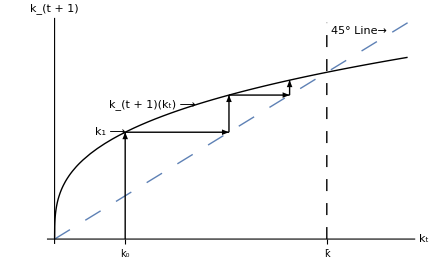

Exporting figure to ../../Figures/OLGModelDynamics.pdf

```mathematica
Initialk=0.01;ArrowHeadSize=0.025;
SteadyStateLine = Graphics[{Dashing[{0.02}],Line[{{kBar,0},{kBar,kMax}}]}];
InitialPoint = Graphics[{Thickness[Medium],Arrowheads[{{ArrowHeadSize,1,-Graphics-}}],Arrow[{{Initialk,0},{Initialk,NextStepk[Initialk]}}]}];OLGModelDynamics = Show[
PlotOLG
,Degree45
,InitialPoint
,NextStepArrows[NextStepk[.01],ArrowHeadSize]
,NextStepArrows[.01,ArrowHeadSize]
,SteadyStateLine
,Graphics[Text["45° Line→",{.047,.047},{1,-1}]]
,Graphics[Text["k_1 ⟶ ",{Initialk,NextStepk[Initialk]},{1,0}]]
,Graphics[Text["k_(t + 1)(k_t) ⟶ ",{.02,NextStepk[.02]},{1,0}]]
,ImageSize->{72 6.,72 6./GoldenRatio}
,AxesLabel->{"k_t","k_(t + 1)"}
,Ticks->{{{kBar,"k̄"},{Initialk,"k_0"}},None}
];
ExportFigsToDir["OLGModelDynamics",FigDir];
```

```mathematica
(* Now analyze model described in handout SocSecAndKAccum *)
```

```mathematica
NextStepk[k_] := 𝒬 k^ε-.013;
Print[kBarBar = (kSeek/. FindRoot[kSeek ==  𝒬 kSeek^ε - .013,{kSeek,.01,.03}])];
```

0.0156082

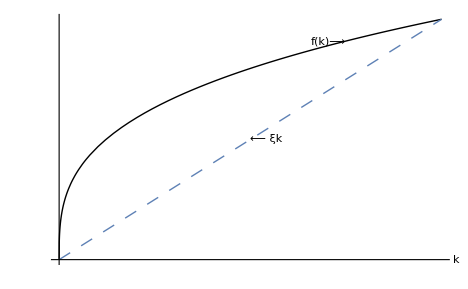

Exporting figure to ../../Figures/fAndnkPlot.pdf

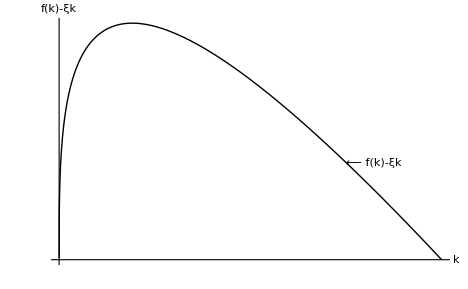

Exporting figure to ../../Figures/fMinusnkPlot.pdf

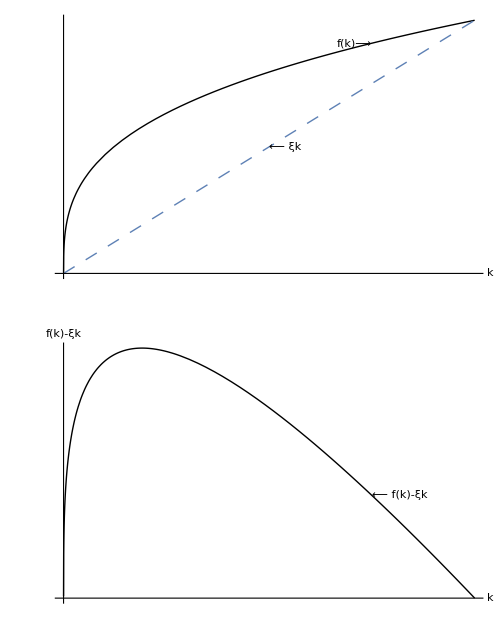

Exporting figure to ../../Figures/fnkBoth.pdf

```mathematica
kBarForcMax=(ξ/ε)^(1/(ε-1));
kBarForcZero=ξ^(1/(ε-1));
fBase=Plot[k^ε,{k,0,kBarForcZero}];
nkBase=Plot[ξ  k,{k,0,kBarForcZero},PlotStyle->{Thickness[Medium],Dashing[{0.02}]}];
fAndnkPlot=Show[fBase
,nkBase
,Graphics[Text["⟵ ξk",{kBarForcZero/2, ξ kBarForcZero/2},{-1,0}]]
,Graphics[Text["f(k)⟶",{kBarForcZero(3/4),( kBarForcZero(3/4))^ε},{1,0}]]
,AxesLabel->{"k","        "}
,Ticks->None];
fMinusnkBase=Plot[{k^ε-ξ  k},{k,0,kBarForcZero}];
fMinusnkPlot=Show[fMinusnkBase
,Graphics[Text["⟵ f(k)-ξk",{kBarForcZero(3/4),(kBarForcZero(3/4))^ε- ξ kBarForcZero(3/4)},{-1,0}]]
,AxesLabel->{"k","f(k)-ξk"},Ticks->None];
fnkBoth=Show[GraphicsGrid[{{fAndnkPlot},{fMinusnkPlot}}]];
ExportFigsToDir["fAndnkPlot",FigDir];
ExportFigsToDir["fMinusnkPlot",FigDir];
ExportFigsToDir["fnkBoth",FigDir];
```

```mathematica
NewSteadyStateLine = Graphics[{Dashing[{0.02}],Line[{{kBarBar,0},{kBarBar,kMax}}]}];
PlotOLGwSS = Plot[ NextStepk[k],{k,0,kMax},Ticks->None];
OriginalSSPoint = Graphics[{Thickness[Medium],Arrowheads[{{ArrowHeadSize,1,-Graphics-}}],Arrow[{{kBar,kBar},{kBar,NextStepk[kBar]}}]}];
```

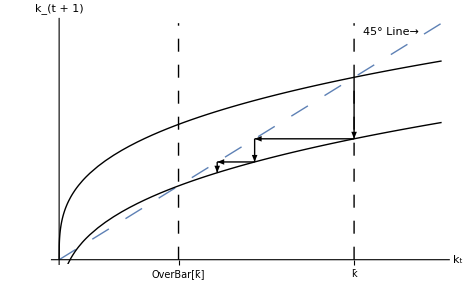

Exporting figure to ../../../SocSecAndKAccum/Figures/SocSecAndKAccum.pdf

```mathematica
(* Generates figures for handout on Social Security and capital accumulation *)
SocSecAndKAccum = Show[PlotOLG
,Degree45
,PlotOLGwSS
,OriginalSSPoint
,Graphics[Text["45° Line→",{.047,.047},{1,-1}]]
,SteadyStateLine
,NewSteadyStateLine
,NextStepArrows[kBar,NextStepk[kBar]]
,NextStepArrows[NextStepk[kBar],ArrowHeadSize]
,AxesLabel->{"k_t","k_(t + 1)"}
,Ticks->{{{kBarBar,"OverBar[k̄]"},{kBar,"k̄"}},None}
];
ExportFigsToDir["SocSecAndKAccum","../../../SocSecAndKAccum/Figures"];
```

```mathematica
(* Now produce graphs used in OLG problem set/exam questions *)
```

```mathematica
(* Effect of a sudden permanent increase in growth *)
```

```mathematica
Ξ = 1.0^YearsPerGeneration;
ξ=Ξ-1;
β = .96^YearsPerGeneration;
𝔊=1.01^YearsPerGeneration;
𝔤=𝔊-1;
𝒬 = (1-ε)(β/(1+β))/𝔊;
kBar = 𝒬^(1/(1-ε));
PlotOLG = Plot[ 𝒬 k^ε,{k,0,kMax}
,Ticks->None
,PlotRange->{{0,kMax},{0,kMax}}
];
```

```mathematica
InitialSteadyStateLine = Graphics[{Dashing[{0.02}],Line[{{kBar,0},{kBar,kMax}}]}];
𝔊=1.03^YearsPerGeneration;
𝔤=𝔊-1;
𝒬=𝒬New = (1-ε)(β/(1+β))/𝔊;
kBarNew = 𝒬^(1/(1-ε));

PlotOLGNew = Plot[ 𝒬New k^ε,{k,0,kMax}
,Ticks->None
,PlotRange->{{0,kMax},{0,kMax}}
];
```

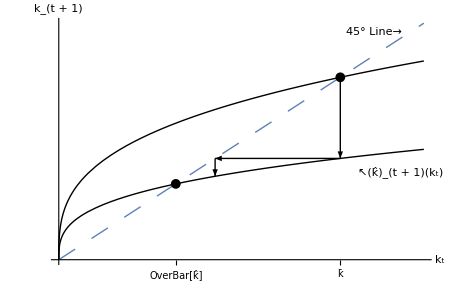

```mathematica
NextStepk[k_] := 𝒬 k^ε;
InitialPoint=Graphics[{PointSize[0.015],Point[{kBar,kBar}]}];
FinalPoint=Graphics[{PointSize[0.015],Point[{kBarNew,kBarNew}]}];
 
InitialJump = Graphics[{Arrowheads[{{ArrowHeadSize,1,-Graphics-}}],Arrow[{{kBar,kBar},{kBar,NextStepk[kBar]}}]}];
Print[OLGGorNShockConverge = Show[
PlotOLG
,Degree45
,PlotOLGNew
,InitialPoint
,FinalPoint
,InitialJump
,NextStepArrows[kBar,ArrowHeadSize]
,Graphics[Text["45° Line→",{.047,.047},{1,-1}]]
,Graphics[Text["↖(k̂)_(t + 1)(k_t)",{.041,NextStepk[.02]},{-1,-1}]]
,AxesLabel->{"k_t","k_(t + 1)"}
,Ticks->{{{kBar,"k̄"},{kBarNew,"OverBar[k̂]"}},None}
]];
```

```mathematica
ExportFigsToDir["OLGGorNShockConverge",FigDir];
```

-Graphics-

Exporting figure to ../../Figures/OLGGorNShockConverge.pdf